```mathematica
Solve[{d==t^2/4,d^2+t^2==1},{d,t}]
```

{{d→-2+√5,t→-2 √(-2+√5)},{d→-2+√5,t→2 √(-2+√5)},{d→-2-√5,t→-2 ⅈ √(2+√5)},{d→-2-√5,t→2 ⅈ √(2+√5)}}

```mathematica
N[{{d->-2+√5,t->-2 √(-2+√5)},{d->-2+√5,t->2 √(-2+√5)},{d->-2-√5,t->-2 ⅈ √(2+√5)},{d->-2-√5,t->2 ⅈ √(2+√5)}}]
```

{{d→0.236068,t→-0.971737},{d→0.236068,t→0.971737},{d→-4.23607,t→0.-4.11634 ⅈ},{d→-4.23607,t→0.+4.11634 ⅈ}}

```mathematica
∫_0^(2 √(-2+√5)) (√(1-t^2)-t^2/4)ⅆt
```

-2/3 (-2+√5)^(3/2)+√(-38+17 √5)+1/2 ArcSin[2 √(-2+√5)]

```mathematica
N[-2/3 (-2+√5)^(3/2)+√(-38+17 √5)+1/2 ArcSin[2 √(-2+√5)]]
```

0.704472

```mathematica
%/Pi
```

0.22424

```mathematica
1-.5-2*%
```

0.0515191

```mathematica
1/2+2*.22424+1*0.05152
```

1.

```mathematica
A=Table[RandomReal[{-1,1},{2,2}],{x,1,1000000}];
```

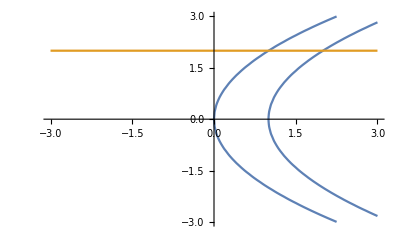

```mathematica
Show[ListPlot[Table[{Det[A[[a]]],Tr[A[[a]]]},{a,1,Length[A]}],PlotStyle->Red],ContourPlot[t^2-4d==0,{d,-3,3},{t,-3,3},AspectRatio->1],ContourPlot[{t^2/4+1==d,t==2},{d,-3,3},{t,-3,3}],PlotRange->All]
```

```mathematica
B=Table[RandomVariate[NormalDistribution[],{2,2}],{x,1,1000000}];
```

```mathematica
Show[ListPlot[Table[{Det[B[[a]]],Tr[B[[a]]]},{a,1,Length[B]}],PlotStyle->Red],ContourPlot[t^2-4d==0,{d,-10,10},{t,-10,10},AspectRatio->1],PlotRange->All]
```

-Graphics-

```mathematica
Solve[{g*i*n-g*a*n^2-g*b*n*m-k*n==0,h*i*m-g*a*n*m-h*b*m^2-l*m==0},{n,m}]
```

{{n→-(-g i+k)/(a g),m→0},{n→0,m→0},{n→0,m→-(-h i+l)/(b h)},{n→-(-h k+g l)/(a g (g-h)),m→-(-g i+h i+k-l)/(b (g-h))}}

```mathematica
Length[%]
```

4

```mathematica
Roots[(e*A-g*A^3)/t==0,A]
```

A==0||A==(√e)/(√g)||A==-(√e)/(√g)

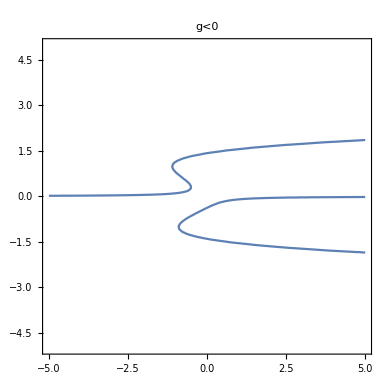
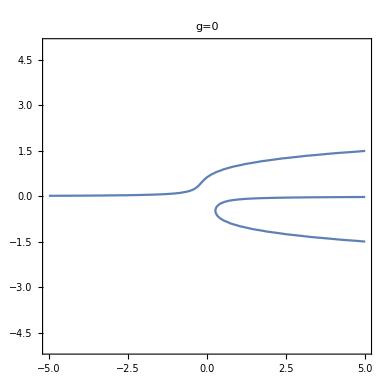
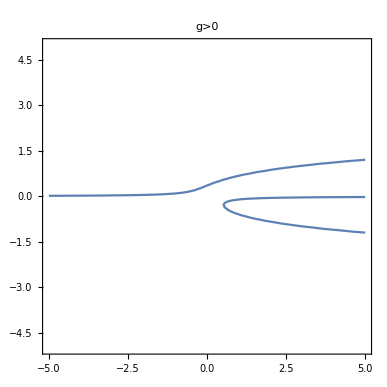

```mathematica
{ContourPlot[.1+e*A+2*A^3-A^5==0,{e,-5,5},{A,-5,5},PlotLabel->"g<0"],ContourPlot[.1+e*A+0*A^3-A^5==0,{e,-5,5},{A,-5,5},PlotLabel->"g=0"],ContourPlot[.1+e*A-2*A^3-A^5==0,{e,-5,5},{A,-5,5},PlotLabel->"g>0"]}
```